```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
PortfolioChart[stocks_,start_,end_]:=Module[{s,portfolio,data,symbols},
s=NormalizeData[#,start,end]&/@stocks;
portfolio=Transpose@{s[[1]][[All,1]],Mean/@Transpose@(#[[All,2]]&/@s)};
data=s~Join~{portfolio};
symbols=stocks~Join~{"portfolio"};
DateListPlot[data,PlotLegends->symbols,PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[5, "Years"]];
start1=DatePlus[Today,-Quantity[1, "Years"]];
start2=DatePlus[Today,-Quantity[2, "Years"]];
end=Today;
end//DateString
```

Tue 14 Mar 2017

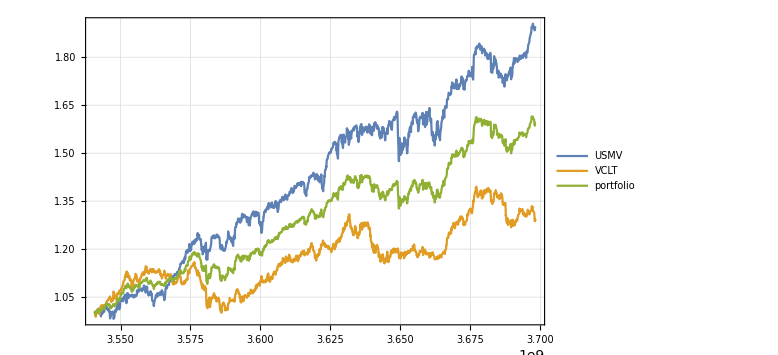

```mathematica
PortfolioChart[{"USMV","VCLT"},start,end]
```

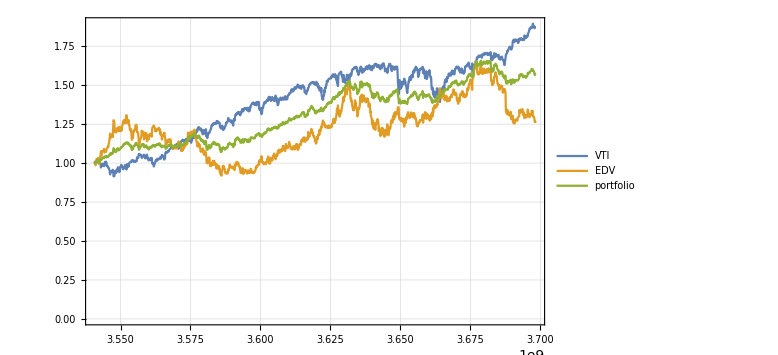

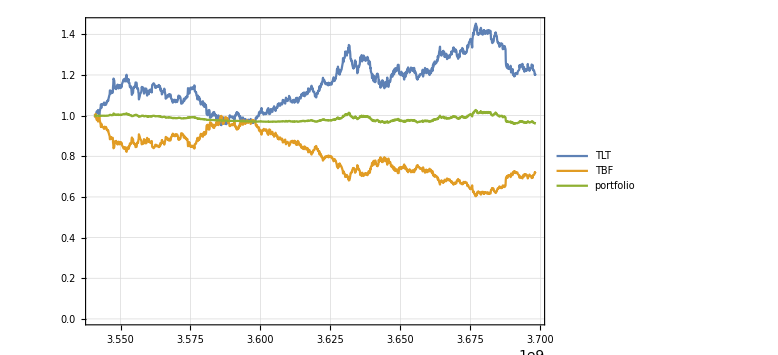

```mathematica
PortfolioChart[{"VTI","EDV"},start,end]
PortfolioChart[{"TLT","TBF"},start,end]
```

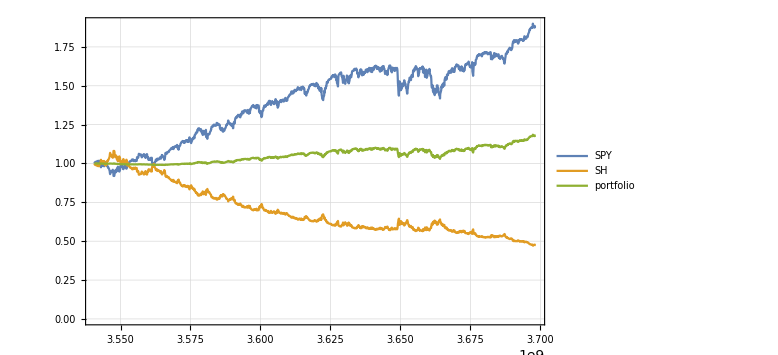

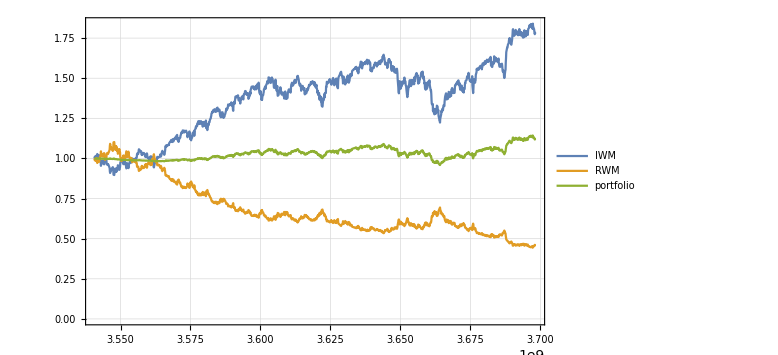

```mathematica
PortfolioChart[{"SPY","SH"},start,end]
PortfolioChart[{"IWM","RWM"},start,end]
```

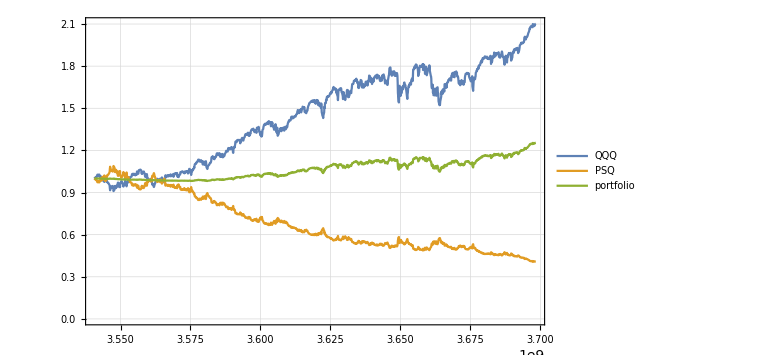

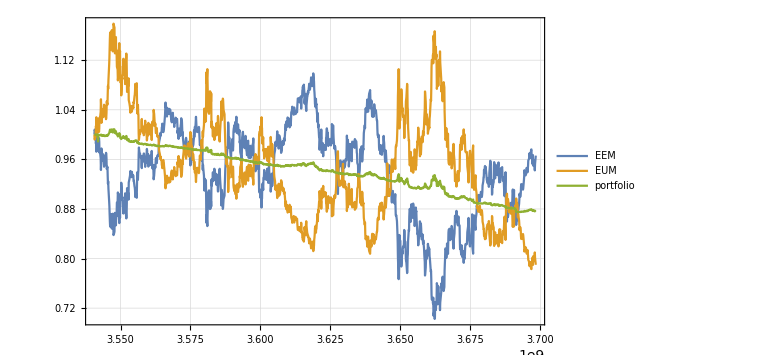

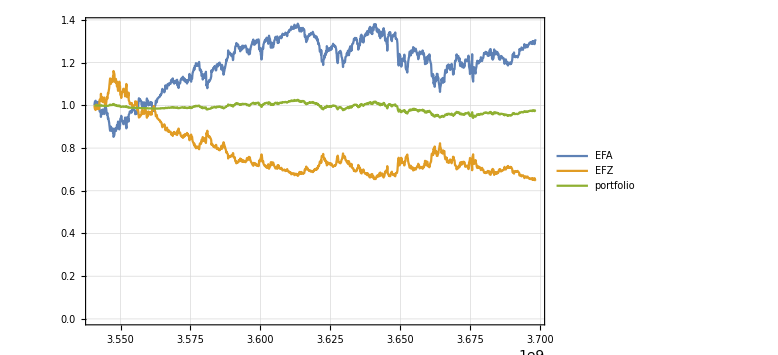

```mathematica
PortfolioChart[{"QQQ","PSQ"},start,end]
PortfolioChart[{"EEM","EUM"},start,end]
PortfolioChart[{"EFA","EFZ"},start,end]
```

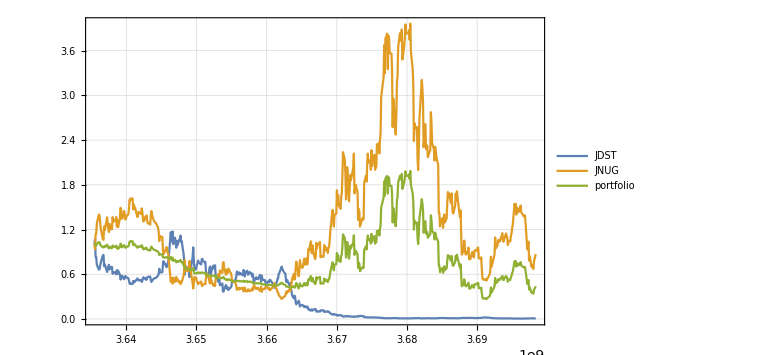

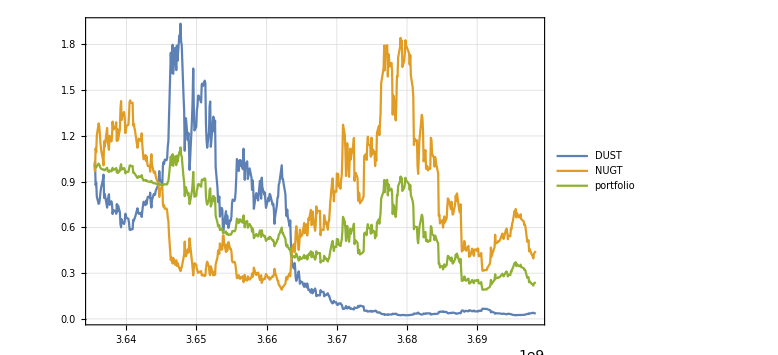

```mathematica
PortfolioChart[{"JDST","JNUG"},start2,end]
PortfolioChart[{"DUST","NUGT"},start2,end]
```

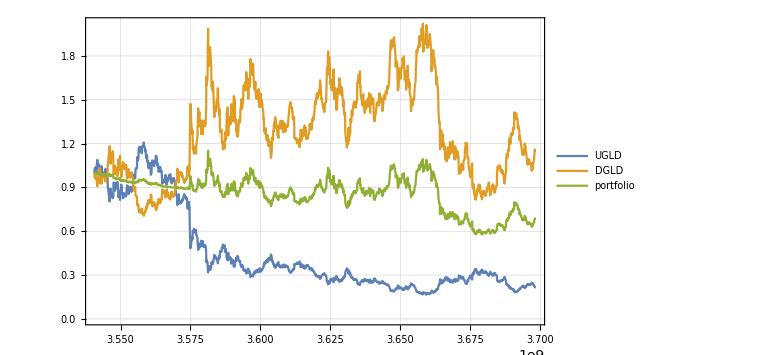

```mathematica
PortfolioChart[{"UGLD","DGLD"},start,end]
```

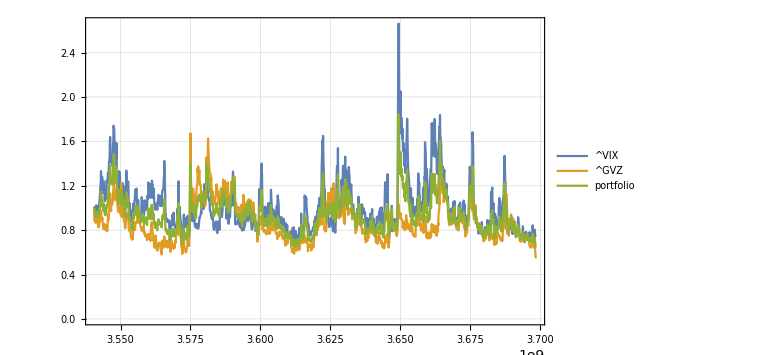

```mathematica
PortfolioChart[{"^VIX","^GVZ"},start,end]
```